## Appendix A3 (Effect of conditioning strength of coexistence outcomes)

### Setup

```mathematica
ClearAll["α","β","f","g"]
```

```mathematica
f[ν_,σ_,ζ_]:=ν NIntegrate[Exp[(-(x+ζ)^2)/σ^2]Exp[(-(x-ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[(-(x+ζ)^2)/σ^2]^2,{x,-Infinity,Infinity}]
```

```mathematica
g[ν_,σ_,ζ_]:=ν NIntegrate[Exp[(-(x+ζ)^2)/σ^2]Exp[(-(x+ζ)^4)/(81 σ^4)],{x,-Infinity,Infinity}]/NIntegrate[Exp[(-(x+ζ)^2)/σ^2]^2,{x,-Infinity,Infinity}]
```

#### Dynamics

```mathematica
Subscript[dN, 1]:=Subscript[N, 1](1-(S+ϵ)^4/ω^4-( β Subscript[N, 1]+α Subscript[N, 2]));
Subscript[dN, 2]:=Subscript[N, 2](1-(S-ϵ)^4/ω^4-(α Subscript[N, 1]+β Subscript[N, 2]));
dS:=η(-ϵ-S)Subscript[N, 1]+η(ϵ-S)Subscript[N, 2];
```

```mathematica
Jc={{D[Subscript[dN, 1],Subscript[N, 1]],D[Subscript[dN, 1],Subscript[N, 2]],D[Subscript[dN, 1],S]},{D[Subscript[dN, 2],Subscript[N, 1]],D[Subscript[dN, 2],Subscript[N, 2]],D[Subscript[dN, 2],S]},{D[dS,Subscript[N, 1]],D[dS,Subscript[N, 2]],D[dS,S]}};
```

#### Equilibrium

```mathematica
eqN=FullSimplify[Solve[Subscript[dN, 1]==0&&Subscript[dN, 2]==0,{Subscript[N, 1],Subscript[N, 2]}]]
```

{{N_1→0,N_2→0},{N_1→0,N_2→(-(S-ϵ)^4+ω^4)/(β ω^4)},{N_1→(S^4 (-α+β)+4 S^3 (α+β) ϵ+6 S^2 (-α+β) ϵ^2+4 S (α+β) ϵ^3+(α-β) (-ϵ^4+ω^4))/((α-β) (α+β) ω^4),N_2→(S^4 (-α+β)-4 S^3 (α+β) ϵ+6 S^2 (-α+β) ϵ^2-4 S (α+β) ϵ^3+(α-β) (-ϵ^4+ω^4))/((α-β) (α+β) ω^4)},{N_1→(-(S+ϵ)^4+ω^4)/(β ω^4),N_2→0}}

### Figure A2(a) - Weak conditioning

```mathematica
ClearAll["pars"]
```

```mathematica
pars={ω->1,σ->1,ν->1,η->0.1,ζ->1,ϵ->0.3};
α=f[ν/.pars,σ/.pars,ζ/.pars]
β=g[ν/.pars,σ/.pars,ζ/.pars]
```

1.06713

1.40176

```mathematica
x0=0.1;y0=0.1;z0=0.5; T=150; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

```mathematica
nsol=NDSolve[{D[x[t],t]==dx,D[y[t],t]==dy,D[z[t],t]==dz,x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
```

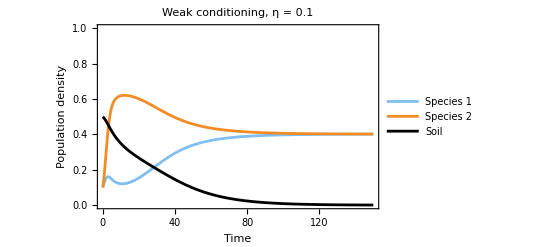

```mathematica
figA2a=Plot[{x[t]/.nsol,y[t]/.nsol,z[t]/.nsol},{t,0,T},PlotRange->{0,1},PlotStyle->{RGBColor[0.5016764639999998, 0.7492700575999999, 0.9393325664],RGBColor[0.9529226912, 0.55, 0.14],Black},PlotLegends->Placed[{"Species 1","Species 2","Soil"},{Right,Top}],Frame->True,FrameLabel->{"Time","Population density"},LabelStyle->{FontSize->15,FontColor->Black},PlotLabel->Style["Weak conditioning, η = 0.1",FontSize->20]]
```

```mathematica
eqNSol=FullSimplify[Solve[N[Subscript[dN, 1]/.pars]==0&&N[Subscript[dN, 2]/.pars]==0&&N[dS/.pars]==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{N_1→0.401759,N_2→0.401759,S→0}}

```mathematica
Eigenvalues[Jc/.pars/.eqNSol[[1]]]
```

{-0.9919,-0.165144,-0.0496486}

```mathematica
Eigenvalues[Jc/.pars/.Subscript[N, 1]->(1/β)/.pars/.Subscript[N, 2]->0/.S->-ϵ/.pars]
```

{-1.,0.109122,-0.0713387}

```mathematica
Eigenvalues[Jc/.pars/.Subscript[N, 1]->0/.Subscript[N, 2]->(1/β)/.pars/.S->ϵ/.pars]
```

{-1.,0.109122,-0.0713387}

```mathematica
Export[NotebookDirectory[]<>"figA2a.pdf",figA2a];
```

### Figure A2(a) - Strong conditioning

```mathematica
ClearAll["pars"]
```

```mathematica
pars={ω->1,σ->1,ν->1,η->2,ζ->1,ϵ->0.3};
α=f[ν/.pars,σ/.pars,ζ/.pars]
β=g[ν/.pars,σ/.pars,ζ/.pars]
```

1.06713

1.40176

```mathematica
x0=0.1;y0=0.1;z0=0.5; T=150; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

```mathematica
nsol=NDSolve[{D[x[t],t]==dx,D[y[t],t]==dy,D[z[t],t]==dz,x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
```

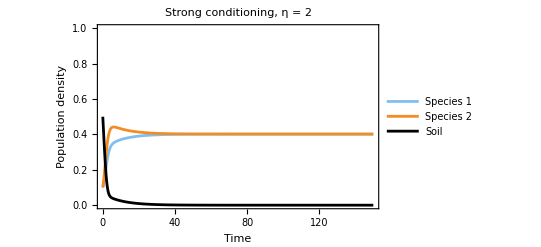

```mathematica
figA2b=Plot[{x[t]/.nsol,y[t]/.nsol,z[t]/.nsol},{t,0,T},PlotRange->{0,1},PlotStyle->{RGBColor[0.5016764639999998, 0.7492700575999999, 0.9393325664],RGBColor[0.9529226912, 0.55, 0.14],Black},PlotLegends->Placed[{"Species 1","Species 2","Soil"},{Right,Top}],Frame->True,FrameLabel->{"Time","Population density"},LabelStyle->{FontSize->15,FontColor->Black},PlotLabel->Style["Strong conditioning, η = 2",FontSize->20]]
```

```mathematica
eqNSol=FullSimplify[Solve[N[Subscript[dN, 1]/.pars]==0&&N[Subscript[dN, 2]/.pars]==0&&N[dS/.pars]==0&&Subscript[N, 1]>0&&Subscript[N, 2]>0,{Subscript[N, 1],Subscript[N, 2],S},Reals]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{N_1→0.401759,N_2→0.401759,S→0}}

```mathematica
Eigenvalues[Jc/.pars/.eqNSol[[1]]]
```

{-1.64158,-0.9919,-0.0998936}

```mathematica
Eigenvalues[Jc/.pars/.Subscript[N, 1]->(1/β)/.pars/.Subscript[N, 2]->0/.S->-ϵ/.pars]
```

{-1.42677,-1.,0.109122}

```mathematica
Eigenvalues[Jc/.pars/.Subscript[N, 1]->0/.Subscript[N, 2]->(1/β)/.pars/.S->ϵ/.pars]
```

{-1.42677,-1.,0.109122}

```mathematica
Export[NotebookDirectory[]<>"figA2b.pdf",figA2b];
```

### Figure A3(a) - Weak conditioning

```mathematica
ClearAll["pars"]
pars={ω->1,σ->1,ν->1,η->0.1,ζ->1};
α=f[ν/.pars,σ/.pars,ζ/.pars]
β=g[ν/.pars,σ/.pars,ζ/.pars]
```

1.06713

1.40176

```mathematica
ϵs =Range[0,1.2,0.01];
nϵ = Length[ϵs];
Ss = Range[-2.2, 2.2, 0.05];
nS = Length[Ss];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nS,3}];
yf=Array[,{nϵ*nS,3}];
yf1=Array[,{nϵ*nS,3}];
yf2=Array[,{nϵ*nS,3}];
yf3=Array[,{nϵ*nS,3}];
zf=Array[,{nϵ*nS,3}];
st=Array[,{nϵ*nS,3}];
```

```mathematica
x0=0.1;y0=0.1; T=1000; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

```mathematica
Timing[
Do[
Do[
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==Ss[[j1]]},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
If[Extract[x[T]/.nsol,1]<-0.001||Extract[y[T]/.nsol,1]<-0.001,
Print[{(x[T]/.nsol),(y[T]/.nsol),Ss[[j1]],ϵs[[j2]]}],
xf[[(j1-1)*nϵ+j2]]=Flatten[{Ss[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{Ss[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{Ss[[j1]],ϵs[[j2]],z[T]/.nsol}];
If[Extract[x[T]/.nsol,1]>0.1&&Extract[y[T]/.nsol,1]>0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],0}];
If[Extract[x[T]/.nsol,1]>0.1&&Extract[y[T]/.nsol,1]<0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],1}];
If[Extract[x[T]/.nsol,1]<0.1&&Extract[y[T]/.nsol,1]>0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],2}];
If[Extract[x[T]/.nsol,1]<0.1&&Extract[y[T]/.nsol,1]<0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],3}];
],
{j2,nϵ}],
{j1,nS}]
]
```

{340.375,Null}

```mathematica
myColor[z_]:=Piecewise[{{RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],0<=z<1},{RGBColor[0.5016764639999998, 0.7492700575999999, 0.9393325664],1<=z<2},{RGBColor[0.9529226912, 0.93983914, 0.6205618136],2<=z<3},{LightGray,z>=3}}]
```

```mathematica
figPSF=ListDensityPlot[st,ColorFunctionScaling->False,ColorFunction->myColor,Frame->True,FrameLabel->{"",""},LabelStyle->{FontSize->15,FontColor->Black}];
```

```mathematica
figA3a=Show[{figPSF,Plot[ω/.pars,{x,-2.2,2.2},PlotStyle->{Dashed,Black}]},Frame->True,FrameLabel->{"Soil origin (E_0)","Δ Soil preference |ϵ_2-ϵ_1|/2"},LabelStyle->{FontSize->20,FontColor->Black},PlotRange->{{-2.2,2.2},{0,1.2}},PlotLabel->Style["Soil conditioning present, η=0.1",FontSize->20],Epilog-> {Inset[Text[Style["Species 1 only ",FontSize->15]],{-1,0.8}],Inset[Text[Style["Coexistence ",FontSize->15]],{0,0.3}],Inset[Text[Style["Species 2 only ",FontSize->15]],{1,0.8}],Inset[Text[Style["Ext. ",FontSize->15]],{-1.85,0.4}],Inset[Text[Style["Ext. ",FontSize->15]],{1.95,0.4}]}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"figA3a.tif",figA3a,ImageResolution->600];
```

### Figure A3(b) - Strong conditioning

```mathematica
ClearAll["pars"]
pars={ω->1,σ->1,ν->1,η->2,ζ->1};
α=f[ν/.pars,σ/.pars,ζ/.pars]
β=g[ν/.pars,σ/.pars,ζ/.pars]
```

1.06713

1.40176

```mathematica
ϵs =Range[0,1.2,0.01];
nϵ = Length[ϵs];
Ss = Range[-2.2, 2.2, 0.05];
nS = Length[Ss];
```

```mathematica
ClearAll["xf","yf","zf"]
```

```mathematica
xf=Array[,{nϵ*nS,3}];
yf=Array[,{nϵ*nS,3}];
yf1=Array[,{nϵ*nS,3}];
yf2=Array[,{nϵ*nS,3}];
yf3=Array[,{nϵ*nS,3}];
zf=Array[,{nϵ*nS,3}];
st=Array[,{nϵ*nS,3}];
```

```mathematica
x0=0.1;y0=0.1; T=1000; 
dx=Subscript[dN, 1]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dy=Subscript[dN, 2]/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
dz=dS/.pars/.{Subscript[N, 1]->x[t],Subscript[N, 2]->y[t],S->z[t]};
```

```mathematica
DOPRIamat={{1/5},{3/40,9/40},{44/45,-56/15,32/9},{19372/6561,-25360/2187,64448/6561,-212/729},{9017/3168,-355/33,46732/5247,49/176,-5103/18656},{35/384,0,500/1113,125/192,-2187/6784,11/84}};
DOPRIbvec={35/384,0,500/1113,125/192,-2187/6784,11/84,0};
DOPRIcvec={1/5,3/10,4/5,8/9,1,1};
DOPRIevec={71/57600,0,-71/16695,71/1920,-17253/339200,22/525,-1/40};
DOPRICoefficients[5,p_]:=N[{DOPRIamat,DOPRIbvec,DOPRIcvec,DOPRIevec},p];
```

```mathematica
Timing[
Do[
Do[
nsol=NDSolve[{D[x[t],t]==(dx/.ϵ->ϵs[[j2]]),D[y[t],t]==(dy/.ϵ->ϵs[[j2]]),D[z[t],t]==(dz/.ϵ->ϵs[[j2]]),x[0]==x0,y[0]==y0,z[0]==Ss[[j1]]},{x,y,z},{t,0,T},Method->{"ExplicitRungeKutta","DifferenceOrder"->5,"Coefficients"->DOPRICoefficients,"StiffnessTest"->False}];
If[Extract[x[T]/.nsol,1]<-0.001||Extract[y[T]/.nsol,1]<-0.001,
Print[{(x[T]/.nsol),(y[T]/.nsol),Ss[[j1]],ϵs[[j2]]}],
xf[[(j1-1)*nϵ+j2]]=Flatten[{Ss[[j1]],ϵs[[j2]],x[T]/.nsol}];
yf[[(j1-1)*nϵ+j2]]=Flatten[{Ss[[j1]],ϵs[[j2]],y[T]/.nsol}];
zf[[(j1-1)*nϵ+j2]]=Flatten[{Ss[[j1]],ϵs[[j2]],z[T]/.nsol}];
If[Extract[x[T]/.nsol,1]>0.1&&Extract[y[T]/.nsol,1]>0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],0}];
If[Extract[x[T]/.nsol,1]>0.1&&Extract[y[T]/.nsol,1]<0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],1}];
If[Extract[x[T]/.nsol,1]<0.1&&Extract[y[T]/.nsol,1]>0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],2}];
If[Extract[x[T]/.nsol,1]<0.1&&Extract[y[T]/.nsol,1]<0.1,st[[(j1-1)*nϵ+j2]]={Ss[[j1]],ϵs[[j2]],3}];
],
{j2,nϵ}],
{j1,nS}]
]
```

{248.563,Null}

```mathematica
myColor[z_]:=Piecewise[{{RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],0<=z<1},{RGBColor[0.5016764639999998, 0.7492700575999999, 0.9393325664],1<=z<2},{RGBColor[0.9529226912, 0.93983914, 0.6205618136],2<=z<3},{LightGray,z>=3}}]
```

```mathematica
figPSF=ListDensityPlot[st,ColorFunctionScaling->False,ColorFunction->myColor,Frame->True,FrameLabel->{"",""},LabelStyle->{FontSize->15,FontColor->Black}];
```

```mathematica
figA3b=Show[{figPSF,Plot[ω/.pars,{x,-2.2,2.2},PlotStyle->{Dashed,Black}]},Frame->True,FrameLabel->{"Soil origin (E_0)","Δ Soil preference |ϵ_2-ϵ_1|/2"},LabelStyle->{FontSize->20,FontColor->Black},PlotRange->{{-2.2,2.2},{0,1.2}},PlotLabel->Style["Soil conditioning present, η=2",FontSize->20],Epilog-> {Inset[Text[Style["Species 1 only ",FontSize->15]],{-1,0.8}],Inset[Text[Style["Coexistence ",FontSize->15]],{0,0.3}],Inset[Text[Style["Species 2 only ",FontSize->15]],{1,0.8}],Inset[Text[Style["Ext. ",FontSize->15]],{-1.85,0.4}],Inset[Text[Style["Ext. ",FontSize->15]],{1.95,0.4}]}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"figA3b.tif",figA3b,ImageResolution->600];
```